```mathematica
Clear["Global`*"]
```

```mathematica
(*Define MSTW initial distributions*)
xu[x_]:= Au*x^(eta1)*(1-x)^(eta2)*(1+ epsu*√x + gammau*x) /. {Au -> 14335/10000, eta1 -> 45232/100000, eta2 -> 30409/10000, epsu -> -23737/10000, gammau -> 89924/10000};
xd[x_]:= Ad*x^(eta3)*(1-x)^(eta4)*(1+ epsd*√x + gammad*x)/. {Ad -> 50903/10000, eta3 -> 71978/100000, eta4 -> 51244/10000, epsd -> -43654/10000, gammad -> 74730/10000};
xs[x_]:= As*x^(deltas)*(1-x)^(etas)*(1+ epss*√x + gammas*x) /. {As -> 59964/100000, deltas -> -16276/100000, etas -> 88801/10000, epss -> -29012/10000, gammas -> 16865/1000};
xdelta[x_]:= Adelta*x^(etadelta)*(1-x)^(etas +2)*(1 + gammadelta*x + deltadelta*x^2) /. {Adelta -> 89413/10000, etadelta -> 18760/10000, etas -> 88801/10000, gammadelta -> 84703/10000, deltadelta -> -36507/1000};
xg[x_]:= Ag*x^(deltag)*(1-x)^(etag)*(1+ epsg*√x + gammag*x) + Agp*x^(deltagp)*(1-x)^(etagp) /. {Ag -> 12216/10000000, deltag -> -83657/100000, etag -> 23882/10000, epsg -> -38997/1000, gammag -> 14455/10, Agp -> 0, deltagp -> 0,  etagp -> 0};
xsplus[x_]:= Aplus*x^(deltas)*(1-x)^(etaplus)*(1+ epss*√x + gammas*x) /. {Aplus -> 10302/100000, deltas -> -16276/100000, etaplus -> 13242/1000, epss -> -29012/10000, gammas -> 16865/1000};
xsminus[x_]:= Aminus*x^(deltaminus)*(1-x)^(etaminus)*(1-x/xzero) /. {Aminus -> -11523/1000000, deltaminus -> 2/10, etaminus -> 10285/1000, xzero -> 17414/1000000};
```

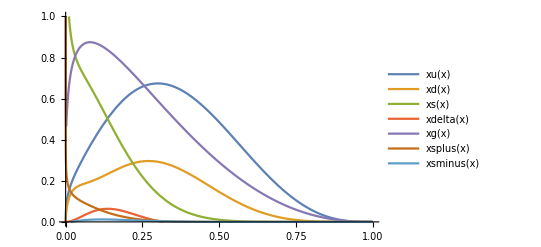

```mathematica
Plot[{xu[x], xd[x], xs[x], xdelta[x], xg[x], xsplus[x], xsminus[x]}, {x,0,1}, PlotLegends->"Expressions", PlotRange->{{0,1}, {0,1}}]
```

```mathematica
u[x_] := xu[x]/x
d[x_] := xd[x]/x
s[x_] := xs[x]/x
delta[x_] := xdelta[x]/x
splus[x_] := xsplus[x]/x
sminus[x_] := xsminus[x]/x
```

```mathematica
(*Define Ellis Stirling distributions at Q0^2 = 1 Gev^2*)
```

```mathematica
(*V_i distributions*)
V1[x_] := u[x] 
V2[x_] := d[x]
V3[x_] := sminus[x]
V4[x_] := 0
V5[x_] := 0
```

```mathematica
(*T_i distributions*)
T3[x_] := u[x] - d[x] - 2*delta[x]
T8[x_] := u[x] + d[x] + s[x] - 3*splus[x]
T15[x_] := u[x] + d[x] + s[x]
T24[x_] := u[x] + d[x] + s[x]
```

```mathematica
(*Singlet and gluon distributions*)
```

```mathematica
Sigma0[x_] := u[x] + d[x] + s[x]
g[x_] := xg[x]/x
```

```mathematica
(*Procedure with V_i*)
```

```mathematica
(*Define anomalous dimension*)
gammaqq[j_] = CF*(-1/2 + 1/(j*(j+1))-2*Sum[1/k, {k,2,j}]) /.CF -> 4/3;
```

```mathematica
(*Mellin transforms*)
MellinV1[j_] = Integrate[x^(j-1)*V1[x], {x,0,1}, Assumptions->{j>1}];
MellinV2[j_] = Integrate[x^(j-1)*V2[x], {x,0,1}, Assumptions->{j>1}];
MellinV3[j_] = Integrate[x^(j-1)*V3[x], {x,0,1}, Assumptions->{j>1}];
MellinV4[j_] = 0;
MellinV5[j_] = 0;
```

```mathematica
(*Define running coupling*)
```

```mathematica
Q0 = 10^9;
Qfinal = 10^11; 
mCharm = 1.4*10^9;
mBottom = 4.75*10^9;
massZ = 91.1876*10^9 ;
alpha0 = 0.68183;
beta0aux3 = 11-2/3*3;
beta0aux4 = 11-2/3*4;
beta0aux5 = 11-2/3*5;

alphaS3[Q2_] := (beta0aux3*Log[Q2/Q0^2] + (4π)/alpha0)^(-1)*(4π);
alphaCharm = alphaS3[mCharm^2];
alphaS4[Q2_] := (beta0aux4*Log[Q2/mCharm^2] + (4π)/alphaCharm)^(-1)*(4π);
alphaBottom = alphaS4[mBottom^2];
alphaS5[Q2_] := (beta0aux5*Log[Q2/mBottom^2] + (4π)/alphaBottom)^(-1)*(4π);

Clear[alphaS]
alphaS[Q2_] = Piecewise[{{alphaS3[Q2],0≤Q2≤mCharm^2},{alphaS4[Q2],mCharm^2≤Q2≤mBottom^2},{alphaS5[Q2],mBottom^2≤Q2≤∞}}];
```

```mathematica
Plot[alphaS[Q2], {Q2, Q0^2, Qfinal^2}]
```

-Graphics-

```mathematica
b3 = (33-2*3)/(12π);
b4 = (33-2*4)/(12π);
b5 = (33-2*5)/(12π);
```

```mathematica
(*Make V_i evolve to Q = mCharm *)
```

```mathematica
MellinV1Ev1[j_, t_] = MellinV1[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
MellinV2Ev1[j_, t_] = MellinV2[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
MellinV3Ev1[j_, t_] = MellinV3[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
MellinV4Ev1[j_, t_] = 0;
MellinV5Ev1[j_, t_] = 0;
```

```mathematica
MellinV1mC[j_] = MellinV1Ev1[j, mCharm^2];
MellinV2mC[j_] = MellinV2Ev1[j, mCharm^2];
MellinV3mC[j_] = MellinV3Ev1[j, mCharm^2];
MellinV4mC[j_] = 0;
MellinV5mC[j_] = 0;
```

```mathematica
(*Make V_i evolve to Q = mBottom *)
```

```mathematica
MellinV1Ev2[j_, t_] = MellinV1mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellinV2Ev2[j_, t_] = MellinV2mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellinV3Ev2[j_, t_] = MellinV3mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellinV4Ev2[j_, t_] = 0;
MellinV5Ev2[j_, t_] = 0;
```

```mathematica
MellinV1mB[j_] = MellinV1Ev2[j, mBottom^2];
MellinV2mB[j_] = MellinV2Ev2[j, mBottom^2];
MellinV3mB[j_] = MellinV3Ev2[j, mBottom^2];
MellinV4mB[j_] = 0;
MellinV5mB[j_] = 0;
```

```mathematica
(*Make V_i evolve to Q = Qfinal *)
```

```mathematica
MellinV1Ev3[j_, t_] = MellinV1mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinV2Ev3[j_, t_] = MellinV2mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinV3Ev3[j_, t_] = MellinV3mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinV4Ev3[j_, t_] = 0;
MellinV5Ev3[j_, t_] = 0;
```

```mathematica
MellinV1f[j_] = MellinV1Ev3[j, Qfinal^2];
MellinV2f[j_] = MellinV2Ev3[j, Qfinal^2];
MellinV3f[j_] = MellinV3Ev3[j, Qfinal^2];
MellinV4f[j_] = 0;
MellinV5f[j_] = 0;
```

```mathematica
(*Calculate inverse Mellin Transforms*)
```

```mathematica
ϕ = 3*π/4;
c = 10;
```

```mathematica
Clear[xV1f]
xV1f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinV1f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

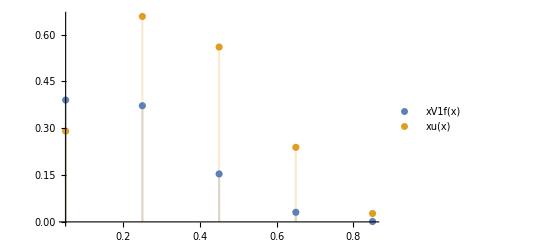

```mathematica
DiscretePlot[{xV1f[x],xu[x]} ,{x,0.05,1, 0.2}, PlotLegends->"Expressions"]
```

```mathematica
Clear[xV2f]
xV2f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinV2f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

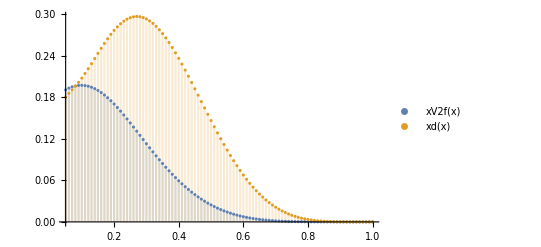

```mathematica
DiscretePlot[{xV2f[x],xd[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
Clear[xV3f]
xV3f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinV3f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

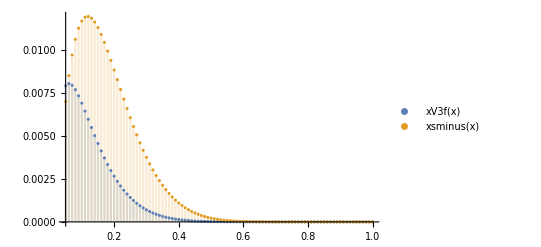

```mathematica
DiscretePlot[{xV3f[x],xsminus[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
(*Procedure with T_i*)
```

```mathematica
(*Mellin transforms*)
MellinT3[j_] = Integrate[x^(j-1)*T3[x], {x,0,1}, Assumptions->{j>1}];
MellinT8[j_] = Integrate[x^(j-1)*T8[x], {x,0,1}, Assumptions->{j>2}];
MellinT15[j_] = Integrate[x^(j-1)*T15[x], {x,0,1}, Assumptions->{j>2}];
MellinT24[j_] = Integrate[x^(j-1)*T24[x], {x,0,1}, Assumptions->{j>2}];
```

```mathematica
(*Make T_i evolve to Q = mCharm*)
```

```mathematica
MellinT3Ev1[j_, t_] = MellinT3[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
MellinT8Ev1[j_, t_] = MellinT8[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
(*MellinT15Ev1[j_, t_] = MellinT15[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));
MellinT24Ev1[j_, t_] = MellinT24[j]*(alpha0/alphaS3[t])^(gammaqq[j]/(2*π*b3));*)
```

```mathematica
MellinT3mC[j_] = MellinT3Ev1[j, mCharm^2];
MellinT8mC[j_] = MellinT8Ev1[j, mCharm^2];
(*MellinT15mC[j_] = MellinT15Ev1[j, mCharm^2];
MellinT24mC[j_] = MellinT24Ev1[j, mCharm^2];*)
```

```mathematica
(*Make T_i evolve to Q = mBottom*)
```

```mathematica
MellinT3Ev2[j_, t_] = MellinT3mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellinT8Ev2[j_, t_] = MellinT8mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
(*MellinT15Ev2[j_, t_] = MellinT15mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellinT24Ev2[j_, t_] = MellinT24mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));*)
```

```mathematica
MellinT3mB[j_] = MellinT3Ev2[j, mBottom^2];
MellinT8mB[j_] = MellinT8Ev2[j, mBottom^2];
(*MellinT15mB[j_] = MellinT15Ev2[j, mBottom^2];
MellinT24mB[j_] = MellinT24Ev2[j, mBottom^2];*)
```

```mathematica
(*Make T_o evolve to Q = Qfinal*)
```

```mathematica
MellinT3Ev3[j_, t_] = MellinT3mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinT8Ev3[j_, t_] = MellinT8mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
(*MellinT15Ev3[j_, t_] = MellinT15mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinT24Ev3[j_, t_] = MellinT24mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));*)
```

```mathematica
MellinT3f[j_] = MellinT3Ev3[j, Qfinal^2];
MellinT8f[j_] = MellinT8Ev3[j, Qfinal^2];
(*MellinT15f[j_] = MellinT15Ev3[j, Qfinal^2];
MellinT24f[j_] = MellinT24Ev3[j, Qfinal^2];*)
```

```mathematica
(*Calculate inverse Mellin transforms*)
```

```mathematica
Clear[xT3f]
xT3f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT3f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

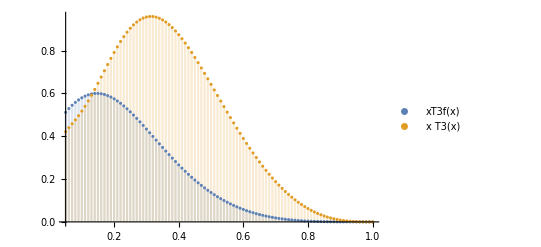

```mathematica
DiscretePlot[{xT3f[x],x*T3[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
Clear[xT8f]
xT8f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT8f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

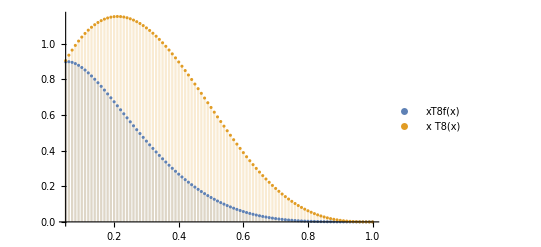

```mathematica
DiscretePlot[{xT8f[x],x*T8[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
(*Clear[xT15f]
xT15f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT15f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];*)
```

```mathematica
(*DiscretePlot[{xT15f[x],x*T15[x]} ,{x,0.01,1, 0.01}, PlotLegends->"Expressions"]*)
```

```mathematica
(*Clear[xT24f]
xT24f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT24f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];*)
```

```mathematica
(*NOW WE START WITH THE SINGLET TERMS*)
```

```mathematica
(*DEFINE LINEAR SYSTEM IN J SPACE*)
```

```mathematica
gammaqg[j_] = TR*(2+j+j^2)/(j*(j+1)*(j+2)) /. TR ->1/2;
gammagq[j_] = CF*(2+j+j^2)/(j*(j^2-1)) /. CF -> 4/3;
gammagg[j_,nf_] = 2*CA*(-1/12 + 1/(j*(j-1)) + 1/((j+1)*(j+2)) - Sum[1/k, {k,2,j}]) - 2/3*nf*TR /. {CA -> 3,TR -> 1/2};
```

```mathematica
Clear[M]
M[j_, nf_] = {{gammaqq[j], 2*nf*gammaqg[j]}, {gammagq[j], gammagg[j, nf]}};
val1[j_, nf_] = Eigenvalues[M[j, nf]][[1]];
val2[j_, nf_] = Eigenvalues[M[j, nf]][[2]];
vec1[j_, nf_] = Eigenvectors[M[j, nf]][[1]];
vec2[j_, nf_] = Eigenvectors[M[j, nf]][[2]];
Diag[j_, nf_] = {{val1[j, nf], 0}, {0,val2[j, nf]}};
P[j_, nf_] = Transpose[{vec1[j, nf], vec2[j, nf]}];
Pinv[j_, nf_] = Inverse[P[j, nf]];
```

```mathematica
(*Procedure with T_15*)
```

```mathematica
(*Make it evolve to Q = mCharm*)
(*Obtain Mellin transform of gluons*)
```

```mathematica
Clear[Melling]
Melling[j_] = Integrate[x^(j-1)*g[x], {x,0,1}, Assumptions->{j>2}];
```

```mathematica
{MellinT15W0[j_], MellingW0[j_]} = Pinv[j, 3].{MellinT15[j], Melling[j]};
```

```mathematica
Clear[PDE1]
PDE1 = D[MellinT15W[j,t], t] == alphaS3[t]/(2*π*t)*val1[j, 3]*MellinT15W[j,t];
```

```mathematica
Clear[PDE2]
PDE2 = D[MellingW[j,t], t] == alphaS3[t]/(2*π*t)*val2[j, 3]*MellingW[j,t];
```

```mathematica
Clear[sol1]
sol1 = DSolve[{PDE1, MellinT15W[j,Q0^2] == MellinT15W0[j]}, MellinT15W[j,t], {j,t}];
```

```mathematica
Clear[sol2]
sol2 = DSolve[{PDE2, MellingW[j,Q0^2] == MellingW0[j]}, MellingW[j,t], {j,t}];
```

```mathematica
Clear[MellinT15Wuse]
MellinT15Wuse[j_,t_]=MellinT15W[j,t]/.sol1[[1]];
```

```mathematica
Clear[MellingWuse]
MellingWuse[j_,t_]=MellingW[j,t]/.sol2[[1]];
```

```mathematica
(*Return to non-diagonal solutions*)
{MellinT15use[j_, t_], Mellinguse[j_,t_]} = P[j,3].{MellinT15Wuse[j,t], MellingWuse[j,t]};
```

```mathematica
(*Make T15 and g evolve to Q = mCharm*)
```

```mathematica
Clear[MellinT15usemC]
Clear[MellingusemC]
MellinT15usemC[j_] = MellinT15use[j,mCharm^2];
MellingusemC[j_] = Mellinguse[j,mCharm^2];
```

```mathematica
(*Make T15 evolve as non-singlet from mCharm*)
MellinT15Ev2[j_, t_] = MellinT15usemC[j] *(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
MellingEv2[j_, t_] = MellingusemC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));
```

```mathematica
(*Make them evolve to mBottom*)
```

```mathematica
MellinT15mB[j_] = MellinT15Ev2[j, mBottom^2];
(*MellingmB[j_] = MellingEv2[j, mBottom^2];*)
```

```mathematica
(*Make T15 and g evolve to Qfinal*)
```

```mathematica
MellinT15Ev3[j_, t_] = MellinT15mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
(*MellingEv3[j_, t_] = MellingmB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));*)
```

```mathematica
MellinT15f[j_] = MellinT15Ev3[j, Qfinal^2];
(*Mellingf[j_] = MellinT24Ev3[j, Qfinal^2];*)
```

```mathematica
(*MellinV1Ev2[j_, t_] = MellinV1mC[j]*(alphaCharm/alphaS4[t])^(gammaqq[j]/(2*π*b4));*)
```

```mathematica
Clear[xT15f]
xT15f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT15f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

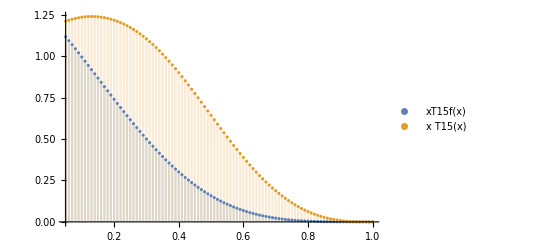

```mathematica
DiscretePlot[{xT15f[x],x*T15[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
(*Procedure with T_24*)
```

```mathematica
(*Below mCharm we have T24 = T15 *)
```

```mathematica
MellinT24mC[j_] = MellinT15use[j,mCharm^2];
MellingmC[j_] = Mellinguse[j, mCharm^2];
```

```mathematica
{MellinT24WmC[j_], MellingWmC[j_]} = Pinv[j,4].{MellinT24mC[j], MellingmC[j]};
```

```mathematica
Clear[PDE3]
PDE3 = D[MellinT24W[j,t], t] == alphaS4[t]/(2*π*t)*val1[j, 4]*MellinT24W[j,t];
```

```mathematica
Clear[PDE4]
PDE4 = D[MellingW2[j,t], t] == alphaS4[t]/(2*π*t)*val2[j, 4]*MellingW2[j,t];
```

```mathematica
Clear[sol3]
sol3 = DSolve[{PDE3, MellinT24W[j,mCharm^2] == MellinT24WmC[j]}, MellinT24W[j,t], {j,t}];
```

```mathematica
Clear[sol4]
sol4 = DSolve[{PDE4, MellingW2[j,mCharm^2] == MellingWmC[j]}, MellingW2[j,t], {j,t}];
```

```mathematica
Clear[MellinT24Wuse]
MellinT24Wuse[j_, t_]= MellinT24W[j,t] /. sol3[[1]];
Clear[MellingW2use]
MellingW2use[j_, t_] = MellingW2[j, t] /. sol4[[1]];
```

```mathematica
(*Return to non-diagonal solution*)
```

```mathematica
{MellinT24use[j_, t_], Melling2use[j_, t_]} = P[j, 4].{MellinT24Wuse[j, t], MellingW2use[j, t]};
```

```mathematica
(*Make T24 and g evolve to Q = mBottom*)
```

```mathematica
Clear[MellinT24mB]
Clear[Melling2mB]
MellinT24mB[j_] = MellinT24use[j,mBottom^2];
Melling2mB[j_] = Melling2use[j,mBottom^2];
```

```mathematica
(*Make T24 evolve as non-singlet from mBottom to Qfinal*)
```

```mathematica
MellinT24Ev3[j_, t_] = MellinT24mB[j]*(alphaBottom/alphaS5[t])^(gammaqq[j]/(2*π*b5));
MellinT24f[j_] = MellinT24Ev3[j, Qfinal^2];
```

```mathematica
Clear[xT24f]
xT24f[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinT24f[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

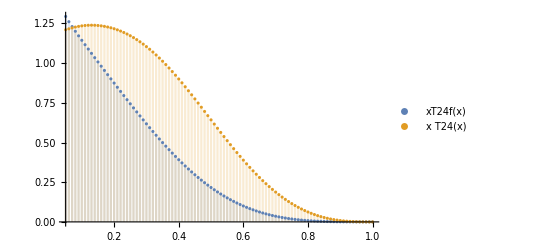

```mathematica
DiscretePlot[{xT24f[x],x*T24[x]} ,{x,0.05,1, 0.01}, PlotLegends->"Expressions"]
```

```mathematica
(*Procedure with singlet Sigma*)
```

```mathematica
MellinSigmamB[j_] = MellinT24use[j, mBottom^2];
MellingmB[j_] = Melling2use[j,mBottom^2];
```

```mathematica
{MellinSigmaWmB[j_], MellingWmB[j_]} = Pinv[j,5].{MellinSigmamB[j], MellingmB[j]};
```

```mathematica
Clear[PDE5]
PDE5 = D[MellinSigmaW[j,t], t] == alphaS5[t]/(2*π*t)*val1[j, 5]*MellinSigmaW[j,t];
```

```mathematica
Clear[PDE6]
PDE6 = D[MellingW3[j,t], t] == alphaS5[t]/(2*π*t)*val2[j, 5]*MellingW3[j,t];
```

```mathematica
Clear[sol5]
sol5 = DSolve[{PDE5, MellinSigmaW[j,mBottom^2] == MellinSigmaWmB[j]}, MellinSigmaW[j,t], {j,t}];
```

```mathematica
Clear[sol6]
sol6 = DSolve[{PDE6, MellingW3[j,mBottom^2] == MellingWmB[j]}, MellingW3[j,t], {j,t}];
```

```mathematica
Clear[MellinSigmaWuse]
MellinSigmaWuse[j_, t_]= MellinSigmaW[j,t] /. sol5[[1]];
Clear[MellingW3use]
MellingW3use[j_, t_] = MellingW3[j, t] /. sol6[[1]];
```

```mathematica
(*Return to non-diagonal solution*)
```

```mathematica
{MellinSigmause[j_, t_], Melling3use[j_, t_]} = P[j, 5].{MellinSigmaWuse[j, t], MellingW3use[j, t]};
```

```mathematica
(*Make Sigma and g evolve to Q = Qfinal*)
```

```mathematica
MellinSigmaf[j_] = MellinSigmause[j, Qfinal^2];
Mellingf[j_] = Melling3use[j, Qfinal^2];
```

```mathematica
Clear[xSigmaf]
xSigmaf[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*MellinSigmaf[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

```mathematica
xSigmaf[.5]
```

0.142205

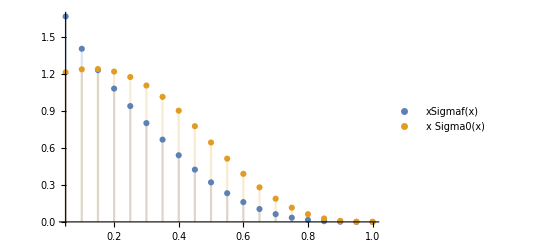

```mathematica
DiscretePlot[{xSigmaf[x],x*Sigma0[x]} ,{x,0.05,1, 0.05}, PlotLegends->"Expressions"]
```

```mathematica
Clear[xgf]
xgf[x_ ? NumericQ] := (1/π)*NIntegrate[Im[Exp[ⅈ*ϕ]*x^(1-c-z*Exp[ⅈ*ϕ])*Mellingf[c+z*Exp[ⅈ*ϕ]]], {z,0,∞}];
```

```mathematica
(*xgf and xSigma take 1min30s per value*)
```

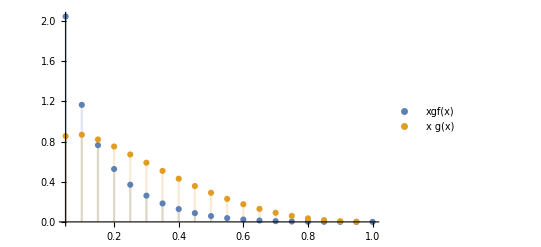

```mathematica
DiscretePlot[{xgf[x],x*g[x]} ,{x,0.05,1, 0.05}, PlotLegends->"Expressions"]
```

```mathematica
(*Now we want to recover the quarks, antiquarks and gluon distributions from V_i, T_iSigma and g*)
```

```mathematica
(*System (V_i, T_i, Sigma) = CvMatrix * (u, ubar, d, dbar, ..., b, bbar) *)
```

```mathematica
CvMatrix = ({{1, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -1}, {1, 1, -1, -1, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, -2, -2, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, -3, -3, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, -4, -4}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}});
```

```mathematica
InvCvMatrix = Inverse[CvMatrix];
```

```mathematica
Inverse[%642]
```

```mathematica
InvCvMatrix // MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 1/4 | 1/12 | 1/24 | 1/40 | 1/10
-1/2 | 0 | 0 | 0 | 0 | 1/4 | 1/12 | 1/24 | 1/40 | 1/10
0 | 1/2 | 0 | 0 | 0 | -1/4 | 1/12 | 1/24 | 1/40 | 1/10
0 | -1/2 | 0 | 0 | 0 | -1/4 | 1/12 | 1/24 | 1/40 | 1/10
0 | 0 | 1/2 | 0 | 0 | 0 | -1/6 | 1/24 | 1/40 | 1/10
0 | 0 | -1/2 | 0 | 0 | 0 | -1/6 | 1/24 | 1/40 | 1/10
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/8 | 1/40 | 1/10
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/8 | 1/40 | 1/10
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/10 | 1/10
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/10 | 1/10)

```mathematica
(*Domain of x-Bjorken*)
xdomain = Table[i, {i,0.01,1,0.01}];
```

```mathematica
(*Results of V1, V2, V3*)
result1 = Map[xV1f, xdomain];
result2 = Map[xV2f, xdomain];
result3 = Map[xV3f, xdomain];

(*Results for T3, T8, T15, T24*)
resultT3 = Map[xT3f, xdomain];
resultT8 = Map[xT8f, xdomain];

resultT15 = Map[xT15f, xdomain];
resultT24 = Map[xT24f, xdomain];

(*Results for singlet and gluon*)
resultSigma = Map[xSigmaf, xdomain];
resultg = Map[xgf, xdomain];
```

```mathematica
(*Results for T3, T8, T15, T24*)
```

```mathematica
(*resultT3 = Map[xT3f, xdomain];
resultT8 = Map[xT8f, xdomain];*)
```

```mathematica
(*resultT15 = Map[xT15f, xdomain];
resultT24 = Map[xT24f, xdomain];*)
```

```mathematica
(*Result for Sigma*)
```

```mathematica
(*resultSigma = Map[xSigmaf, xdomain];*)
```

```mathematica
(*Result for g*)
```

```mathematica
(*resultg = Map[xgf, xdomain];*)
```

```mathematica
(*Define final distributions*)
```

```mathematica
xuFinal = 1/2*result1 + 1/4*resultT3 + 1/12*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
xAntiuFinal = -1/2*result1 + 1/4*resultT3 + 1/12*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
```

```mathematica
xdFinal = 1/2*result2 - 1/4*resultT3 + 1/12*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
xAntidFinal = -1/2*result2 - 1/4*resultT3 + 1/12*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
```

```mathematica
xsFinal = 1/2*result3- 1/6*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
xAntisFinal = -1/2*result3- 1/6*resultT8 + 1/24*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
```

```mathematica
xcFinal =-1/8*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
xAnticFinal =-1/8*resultT15 + 1/40*resultT24 + 1/10*resultSigma;
```

```mathematica
xbFinal = -1/10*resultT24 + 1/10*resultSigma;
xAntibFinal =-1/10*resultT24 + 1/10*resultSigma;
```

```mathematica
(*Create lists to plot*)
```

```mathematica
dataxuFinal =  Transpose@{xdomain, xuFinal};
dataxAntiuFinal =  Transpose@{xdomain, xAntiuFinal};
dataxdFinal  =  Transpose@{xdomain, xdFinal };
dataxAntidFinal=  Transpose@{xdomain, xAntidFinal};
dataxsFinal =  Transpose@{xdomain, xsFinal};
dataxAntisFinal =  Transpose@{xdomain, xAntisFinal};
dataxcFinal =  Transpose@{xdomain, xcFinal};
dataxAnticFinal =  Transpose@{xdomain, xAnticFinal};
dataxbFinal =  Transpose@{xdomain, xbFinal};
dataxAntibFinal =  Transpose@{xdomain, xAntibFinal};
dataxgFinal =  Transpose@{xdomain, resultg};
```

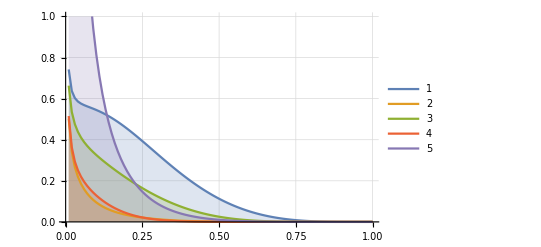

```mathematica
ListPlot[{dataxuFinal, dataxAntiuFinal, dataxdFinal, dataxAntidFinal, dataxgFinal}, PlotLegends->Automatic, PlotStyle-> PointSize[0.012], Joined->True, GridLines->Automatic, Filling->Axis, PlotRange->{{0,1}, {0,1}}]
```

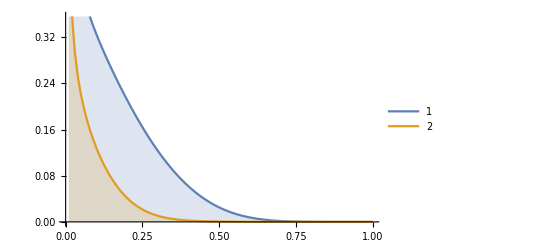

```mathematica
ListPlot[{dataxdFinal, dataxAntidFinal}, PlotLegends->Automatic, Filling->Axis, PlotStyle-> PointSize[0.013], Joined->True]
```

```mathematica
dataxgFinal
```

{{0.01,7.98585},{0.02,4.56422},{0.03,3.17323},{0.04,2.39881},{0.05,1.90073},{0.06,1.5523},{0.07,1.29474},{0.08,1.09678},{0.09,0.940145},{0.1,0.813409},{0.11,0.709032},{0.12,0.621824},{0.13,0.548096},{0.14,0.485144},{0.15,0.430943},{0.16,0.383942},{0.17,0.342936},{0.18,0.30697},{0.19,0.275279},{0.2,0.247242},{0.21,0.222352},{0.22,0.200186},{0.23,0.180394},{0.24,0.162678},{0.25,0.146789},{0.26,0.132511},{0.27,0.119661},{0.28,0.10808},{0.29,0.0976294},{0.3,0.0881899},{0.31,0.079656},{0.32,0.0719351},{0.33,0.0649455},{0.34,0.0586149},{0.35,0.0528792},{0.36,0.047681},{0.37,0.0429694},{0.38,0.0386985},{0.39,0.0348272},{0.4,0.0313187},{0.41,0.0281395},{0.42,0.0252596},{0.43,0.0226519},{0.44,0.0202917},{0.45,0.0181566},{0.46,0.0162264},{0.47,0.0144826},{0.48,0.0129085},{0.49,0.0114887},{0.5,0.0102093},{0.51,0.00905758},{0.52,0.00802198},{0.53,0.00709187},{0.54,0.00625758},{0.55,0.00551026},{0.56,0.00484181},{0.57,0.00424486},{0.58,0.00371264},{0.59,0.00323898},{0.6,0.00281823},{0.61,0.00244525},{0.62,0.00211531},{0.63,0.00182413},{0.64,0.00156777},{0.65,0.00134266},{0.66,0.00114554},{0.67,0.000973441},{0.68,0.000823665},{0.69,0.000693758},{0.7,0.000581493},{0.71,0.000484853},{0.72,0.000402011},{0.73,0.000331318},{0.74,0.000271285},{0.75,0.000220574},{0.76,0.000177981},{0.77,0.000142427},{0.78,0.000112951},{0.79,0.0000886938},{0.8,0.000068893},{0.81,0.0000528745},{0.82,0.000040044},{0.83,0.0000298801},{0.84,0.0000219276},{0.85,0.0000157917},{0.86,0.0000111316},{0.87,7.65589×10^-6},{0.88,5.11713×10^-6},{0.89,3.3074×10^-6},{0.9,2.05397×10^-6},{0.91,1.21532×10^-6},{0.92,6.77363×10^-7},{0.93,3.49984×10^-7},{0.94,1.63762×10^-7},{0.95,6.69238×10^-8},{0.96,2.24809×10^-8},{0.97,5.54085×10^-9},{0.98,7.76629×10^-10},{0.99,2.74818×10^-11},{1.,-1.05691×10^-19}}

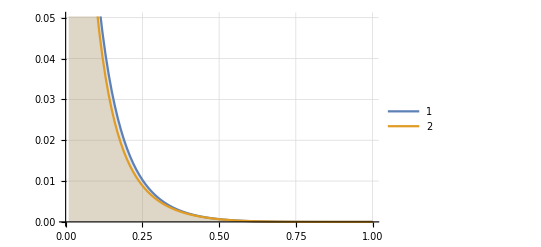

```mathematica
ListPlot[{dataxsFinal, dataxAntisFinal}, PlotLegends->Automatic, GridLines->Automatic, Filling->Axis, PlotStyle-> PointSize[0.013], Joined->True]
```

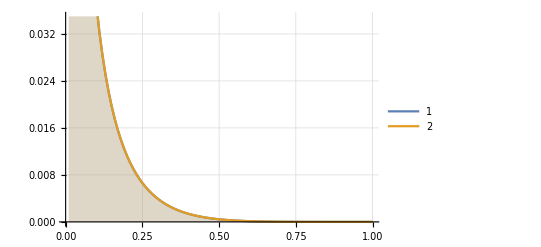

```mathematica
ListPlot[{dataxcFinal, dataxAnticFinal}, PlotLegends->Automatic, GridLines->Automatic, Filling->Axis, PlotStyle-> PointSize[0.013], Joined->True]
```

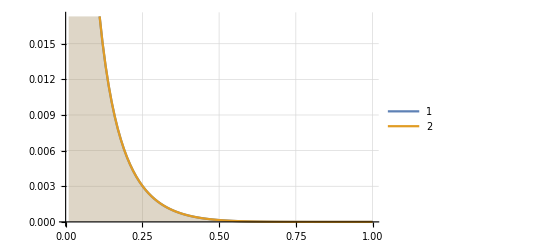

```mathematica
ListPlot[{dataxbFinal, dataxAntibFinal}, PlotLegends->Automatic, Filling-> Axis, GridLines->Automatic, PlotStyle-> PointSize[0.013], Joined->True]
```

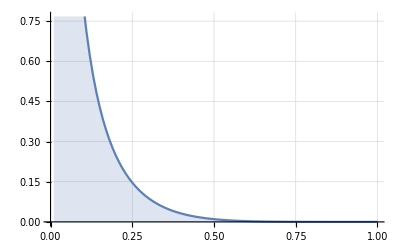

```mathematica
ListPlot[{dataxgFinal}, PlotLegends->Automatic, GridLines->Automatic, Filling->Axis, PlotStyle-> PointSize[0.013], Joined->True]
```

```mathematica
(*Check sum rules *)
```

```mathematica
MellinV1f[1]
```

2.00007

```mathematica
MellinV2f[1]
```

1.

```mathematica
N[MellinV1[1]]
```

2.00007

```mathematica
N[MellinV2[1]]
```

1.

```mathematica
(*Naive momentum sum rule*)
MellinV1f[2] + MellinV2f[2] + Mellingf[2] + 2*((-1/2*MellinV1f[2] + 1/4*MellinV3f[2] + 1/12*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + (-1/2*MellinV2f[2] - 1/4*MellinV3f[2] + 1/12*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) ) + (1/2*MellinV3f[2] - 1/6*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + (-1/2*MellinV3f[2] - 1/6*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2])
```

0.935765

```mathematica
(*Correct momentum sum rule*)
MellinV1f[2] + MellinV2f[2] + Mellingf[2] + 2*((-1/2*MellinV1f[2] + 1/4*MellinV3f[2] + 1/12*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + (-1/2*MellinV2f[2] - 1/4*MellinV3f[2] + 1/12*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) ) + (1/2*MellinV3f[2] - 1/6*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + (-1/2*MellinV3f[2] - 1/6*MellinT8f[2] + 1/24*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + 2*(-1/8*MellinT15f[2] + 1/40*MellinT24f[2] + 1/10*MellinSigmaf[2]) + 2*(-1/10*MellinT24f[2] + 1/10*MellinSigmaf[2])
```

1.00002

```mathematica
xuInital[x_] := x*(1/2*V1[x] + 1/4*T3[x] + 1/12*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
xAntiuInitial[x_] := x*(-1/2*V1[x] + 1/4*T3[x] + 1/12*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
```

```mathematica
xdInitial[x_] := x*(1/2*V2[x] - 1/4*T3[x] + 1/12*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
xAntidInitial[x_] := x*(-1/2*V2[x] - 1/4*T3[x] + 1/12*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
```

```mathematica
xsInitial[x_] := x*(1/2*V3[x]- 1/6*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
xAntisInitial[x_] := x*(-1/2*V3[x]- 1/6*T8[x] + 1/24*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
```

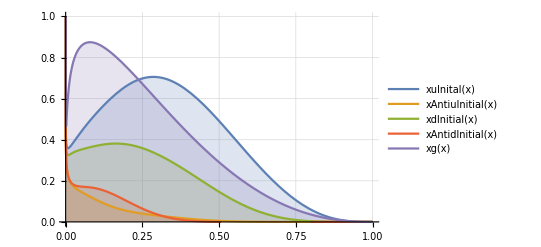

```mathematica
Plot[{xuInital[x], xAntiuInitial[x], xdInitial[x], xAntidInitial[x], xg[x]}, {x,0,1}, Filling->Axis, GridLines->Automatic, PlotRange->{{0,1}{0,1}}, PlotLegends->"Expressions"]
```

```mathematica
NIntegrate[xuInital[x] + xAntiuInitial[x] + xdInitial[x] + xAntidInitial[x] + xg[x] + xsInitial[x] + xAntisInitial[x], {x,0,1}]
```

1.00002

```mathematica
xcInitial[x_] :=x*(-1/8*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
xAnticInitial[x_] :=x*(-1/8*T15[x] + 1/40*T24[x] + 1/10*Sigma0[x]);
```

```mathematica
xbInitial[x_] :=x*(-1/10*T24[x] + 1/10*Sigma0[x]);
xAntibInitial[x_] :=x*(-1/10*T24[x] + 1/10*Sigma0[x]);
```

```mathematica
zero[x_] := 0;
```

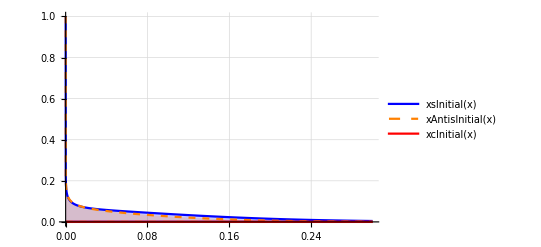

```mathematica
Plot[{xsInitial[x], xAntisInitial[x], xcInitial[x], xAnticInitial[x], xbInitial[x], xAntibInitial[x]}, {x,0,.3}, GridLines->Automatic, PlotRange->{{0,1}{0,1}}, PlotLegends->"Expressions", PlotStyle-> {Blue, Directive[Orange, Dashed], Red}, Filling -> Axis]
```

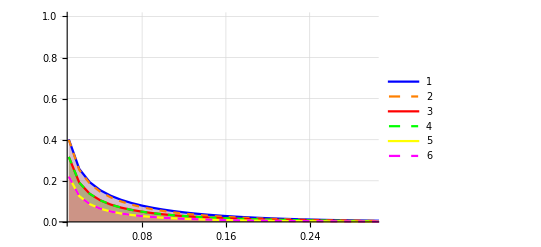

```mathematica
ListPlot[{dataxsFinal, dataxAntisFinal, dataxcFinal, dataxAnticFinal,dataxbFinal, dataxAntibFinal}, PlotLegends->Automatic, PlotStyle-> {Blue, Directive[Orange, Dashed], Red,
Directive[Green, Dashed], Yellow,Directive[Magenta, Dashed]}, Joined->True, GridLines->Automatic, Filling->Axis, PlotRange->{{.007,.3}, {0,1}}]
```

```mathematica
Mellingf[2]
```

0.490124

```mathematica
N[Melling[2]]
```

0.362238

```mathematica
N[Mellinu[2]]
```

Mellinu[2.]